# A Model for Fisheries Management

In 2018, 294,300 tonnes of fish were harvested in British Columbia valued at ~$1.3 Billion.  Proactively managing fisheries is therefore essential for the BC economy. 

Math is particularly necessary and well suited to study the dynamics of and manage populations. 
	First, modelling allows us to test and optimize different management strategies.  
	
	Second, biological populations naturally exhibit non-linear behaviour which can be unintuitive and hard to predict without modelling support.

Goal: Build a suite of models for managing a fish population with harvest.  

In conservation biology, we refer to the removal of individuals through hunting and fishing as “harvest”.

#### Some Preliminaries

```mathematica
MyCol=Table[ColorData["DarkBands"][i/6-0.01],{i,1,6}][[{3,4,6,2,1,5}]]
```

{RGBColor[0.6416497175320824, 0.22039024680361508, 0.2965244160637617],RGBColor[0.6953106517659292, 0.4338224431042085, 0.2550317501625878],RGBColor[0.8884240140546887, 0.8315410617160953, 0.3918643845410284],RGBColor[0.30222321343557096, 0.5283591583672841, 0.26781478622442834],RGBColor[0.23132947583985186, 0.5230171758179645, 0.6762635983204028],RGBColor[0.3208696220556491, 0.33272406933605325, 0.551604665638763]}

```mathematica
Round[List@@@MyCol*255,1]
```

{{164,56,76},{177,111,65},{227,212,100},{77,135,68},{59,133,172},{82,85,141}}

```mathematica
PlotOptions={Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12],LabelStyle->Directive[Black,13]};
PlotTypes={Plot,ListPlot,ListLogPlot,ListLinePlot,DiscretePlot,MatrixPlot};
Do[Map[SetOptions[x,#]&,PlotOptions],{x,PlotTypes}];
```

## Question 1: How does the population grow in the absence of harvest?

Consider a salmon population, salmon are anadromous meaning that they hatch in fresh water, travel to the ocean as juveniles and return to fresh water as adults to spawn.  Individuals of the same species (e.g., coho, chinook) return to their home streams simultaneously.  This results in synchronized reproduction. To model this synchrony in reproduction we use a discrete-time model, using recursion equations to describe the change in the population size from one year to the next.

To develop our intuition for the population dynamics, let’s start by considering first an unstructured model which ignores that fish may be in different developmental ages.

When we model population dynamics of dioecious species (species with two, or more, sexes) we model only the abundance of females as they are the ones who give birth (or lay eggs in the case of salmon). 

Suppose that the probability that an individual female reproduces in a given year is  . 
Similarly, suppose that the probability that an individual dies in a year is .  This probability , increases with the number of individuals in the population due to competition.  If there are  females in year , the number in year  can be written as:



where  is the increasing death rate with increasing population density.

## Question 1a: What are the long-term population size?

To figure out what happens in the long term, we want to ask when the population size is no longer changing (e.g., ).

```mathematica
Solve[{n+b n- d n (1+α n)==n},n]
```

{{n→0},{n→(b-d)/(d α)}}

Mathematica can perform symbolic math, which we can use to solve algebraic equations.

So we have two equilibria, first we have a case of  and .  The first one is the case where the population goes extinct and the second one describes the carrying capacity of the population.

### Question: Under what conditions does the population go extinct?

To answer this question, we want to know when is the extinction equilibrium stable. An equilibrium  of the recursion equation  is stable if

Using Mathematica we can also take symbolic derivatives.

```mathematica
F[n_]:=n+b n- d n (1+α n)
```

```mathematica
λ=Simplify[D[F[n],n]/.{n->0}]
```

1+b-d

We want to know when . Even though this inequality is simple enough that we could manipulate it in our head, let’s use Matheamtica:

Using Mathematica we can also reduce  systems of inequalities.

```mathematica
Reduce[{λ<1,0<d,0<b},b]
```

d>0&&0<b<d

So the extinction equilibrium is unstable if  (birth is less then death).  This makes sense!

## Question 1b: What are the transient population dynamics?

But what if we want to know about the transient dynamics?  We could try to solve for the general solution. But this is a non-linear recursion equation so like many non-linear recursion equations we don’t have a known general solution.  Rather let’s solve for the dynamics numerically, where we specify values for the parameters  and  and the initial condition .

```mathematica
pars1={b->0.2,d->0.12,α->0.02,n0->2};
```

```mathematica
Clear[nN]
nN[t_,pars_]:=nN[t,pars]=If[t==0,n0/.pars,nN[t-1,pars]+b nN[t-1,pars]-d nN[t-1,pars](1+α nN[t-1,pars])/.pars]
```

```mathematica
nN[0,pars1]
```

2

```mathematica
nN[1,pars1]
```

2.1504

```mathematica
nN[10,pars1]
```

4.05505

Mathematica has flexible and high quality plotting tools

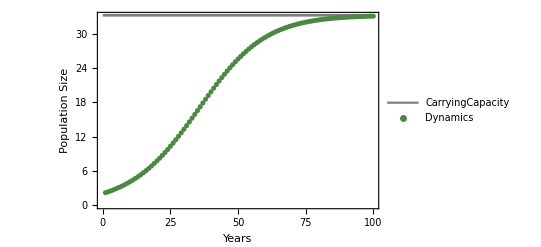

```mathematica
leg1=LineLegend[{Gray},{"CarryingCapacity"}];
leg2=PointLegend[{MyCol[[4]]},{"Dynamics"}];
Show[
(*Dynamics*)
ListPlot[Table[{t,nN[t,pars1]},{t,1,100}],PlotStyle->MyCol[[4]],Frame->True,FrameLabel->{"Years","Population Size"}],
(*Dynamics*)
Plot[(b-d)/(d α)/.pars1,{t0,0,100},PlotStyle->Gray],Epilog->{Inset[leg1,Scaled[{0.75,0.5}]],Inset[leg2,Scaled[{0.75,0.4}]]}]
```

## Question 1c: What if we include randomness in if individuals give birth or die?

The value of  in the deterministic model above can have values ranging from 0 to ∞, and is not constrained to be an integer.  In fact this quantity is actually a measure of population density not population size, and by modelling the system in this way.  If we want to force the population size to be an integer, we then have to consider the randomness in if individuals give birth or if individuals die.  The result is a discrete-time discrete-space Markov process.  To model this let  be the probability that the population has size  at time .  We can visualize how this probability changes using the diagram below.  We can represent this mathematically using a transition probability matrix where element  of this matrix is the probability that we go from having  individuals in time step  to  individuals in time step .

I am not going to explain how we get the matrix P (for that you need to take Math 468 :) )

```mathematica
QMtrx=Table[If[i==j,-b i-d i(1+α i),If[j==i+1,b i,If[j==i-1,d i(1+α i),0]]],{i,0,40},{j,0,40}]/.pars1;
```

```mathematica
{λList,eVecs}=Eigensystem[QMtrx]//Chop;
```

Mathematica can perform matrix algebra both symbolically and numerically.

```mathematica
AMtrx=Transpose[eVecs];
DMtrx=DiagonalMatrix[λList];
DMtrx1=DiagonalMatrix[Exp[λList ]];
AMtrxInv=Inverse[Transpose[eVecs]];
```

```mathematica
PMtrx=AMtrx.DMtrx1.AMtrxInv//Chop;
```

Plotting the P matrix so we can see what it looks like

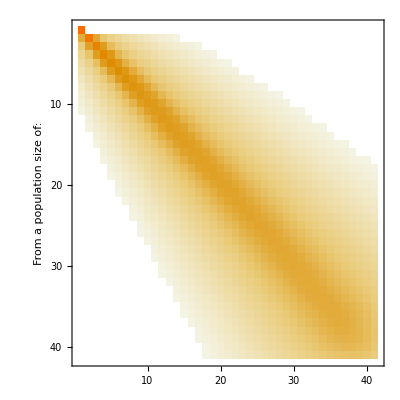

```mathematica
MatrixPlot[PMtrx,FrameLabel->{{None,"To a popualtion size of:"},{"From a population size of:",None}}]
```

We can use this matrix to numerically calculate the probability that the population has a size of  in any given generation.

```mathematica
nList=Table[n,{n,0,40}];
```

```mathematica
X0=Table[If[n==n0/.pars1,1,0],{n,0,40}];
```

```mathematica
Clear[X]
X[t_]:=X[t]=If[t==0,X0,X[t-1].PMtrx]
```

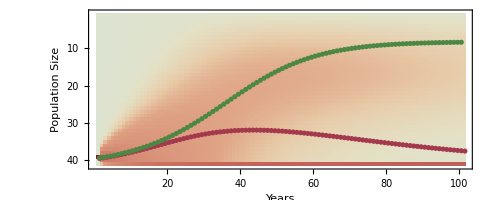

```mathematica
Show[MatrixPlot[Reverse[Transpose[Table[X[t],{t,0,100}]]],ColorFunction->ColorData["ThermometerColors"]],
ListPlot[Table[nList.X[t],{t,0,100}],PlotStyle->MyCol[[1]]],
ListPlot[Table[{t,nN[t,pars1]},{t,1,100}],PlotStyle->MyCol[[4]]],FrameLabel->{"Years","Population Size"}]
```

Here the green is the deterministic solution, the red is the mean of the stochastic model, and the shading is the probability.  From this we can conclude stochasticity lowers population size and often leads to extinction!

Mathematica can be used to run simulations

```mathematica
Clear[PMatrx]
PMatrx[pars_]:=PMatrx[pars]=Block[{nMax,QMtrx,λList,eVecs,AMtrx,DMtrx,DMtrx1,AMtrxInv,PMtrx},
nMax=Round[(b-d)/(d α)*1.2/.pars];
QMtrx=Table[If[i==j,-b i-d i(1+α i),If[j==i+1,b i,If[j==i-1,d i(1+α i),0]]],{i,0,nMax},{j,0,nMax}]/.pars;
{λList,eVecs}=Chop[Eigensystem[QMtrx]];
AMtrx=Transpose[eVecs];
DMtrx=DiagonalMatrix[λList];
DMtrx1=DiagonalMatrix[Exp[λList ]];
AMtrxInv=Inverse[Transpose[eVecs]];
PMtrx=Chop[AMtrx.DMtrx1.AMtrxInv];
PMtrx
]
```

```mathematica
pars1={b->0.2,d->0.12,α->0.02,n0->5};
```

```mathematica
Clear[sim]
sim[pars_,tMax_,intS_]:=sim[pars,tMax,intS]=Block[{out,P,t, nList},P=PMatrx[pars];
nList=Table[n-1,{n,1,Length[P]}];
out={{0,n0/.pars}};
For[t=1,t<=tMax,t++,
AppendTo[out,{t,RandomChoice[P[[out[[-1,2]]+1]]->nList]}]
];
out
]
```

```mathematica
sims=Table[sim[pars1,100,intS],{intS,0,50}];
extinct=Select[sims,#[[-1,2]]==0&];
extant=Select[sims,#[[-1,2]]>0&];
```

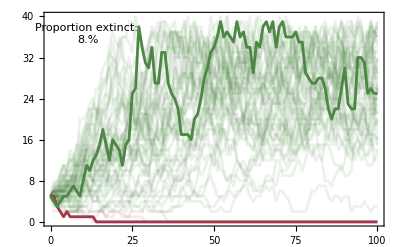

```mathematica
Show[ListLinePlot[extinct,PlotStyle->Directive[MyCol[[1]],Opacity[0.1]]],
ListLinePlot[extant,PlotStyle->Directive[MyCol[[4]],Opacity[0.1]]],ListLinePlot[extinct[[1]],PlotStyle->MyCol[[1]]],ListLinePlot[extant[[1]],PlotStyle->MyCol[[4]]],PlotRange->All,Epilog->Inset["Proportion extinct: \n"<>ToString[Length[extinct]/50*100.0]<>"%",Scaled[{0.13,0.9}]]]
```

## Question 2: What is the effect of a constant versus proportional on population dynamics and extinction potential?

## Constant Harvest

A constant harvest means that we remove a fixed number of individuals every year regardless of the current population size.  This is somewhat like fishing licenses.  Although the number of fishing licenses provided is often based on some estimate of population size, the size of the population is not constantly monitored and estimates can be incorrect or out of date. 

To implement this in our recursion equation we included a constant removal H

```mathematica
pars2={b->0.2,d->0.12,α->0.02,n0->5,hc->0.04};
```

```mathematica
Clear[PMatrxConst]
PMatrxConst[pars_]:=PMatrxConst[pars]=Block[{nMax,QMtrx,λList,eVecs,AMtrx,DMtrx,DMtrx1,AMtrxInv,PMtrx},
nMax=Round[(b-d)/(d α)*1.2/.pars];
QMtrx=Table[If[i==j,-b i-d i(1+α i)-hc i^(1/5),If[j==i+1,b i,If[j==i-1,d i(1+α i)+hc i^(1/5),0]]],{i,0,nMax},{j,0,nMax}]/.pars;
{λList,eVecs}=Chop[Eigensystem[QMtrx]];
AMtrx=Transpose[eVecs];
DMtrx=DiagonalMatrix[λList];
DMtrx1=DiagonalMatrix[Exp[λList ]];
AMtrxInv=Inverse[Transpose[eVecs]];
PMtrx=Chop[AMtrx.DMtrx1.AMtrxInv];
PMtrx
]
```

```mathematica
Clear[sim2]
sim2[pars_,tMax_,intS_]:=sim2[pars,tMax,intS]=Block[{out,P,t, nList},P=PMatrxConst[pars];
nList=Table[n-1,{n,1,Length[P]}];
out={{0,n0/.pars}};
For[t=1,t<=tMax,t++,
AppendTo[out,{t,RandomChoice[P[[out[[-1,2]]+1]]->nList]}]
];
out
]
```

```mathematica
sims2=Table[sim2[pars2,100,intS],{intS,0,50}];
extinct2=Select[sims2,#[[-1,2]]==0&];
extant2=Select[sims2,#[[-1,2]]>0&];
```

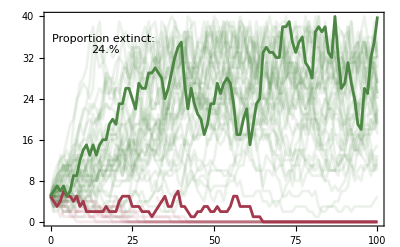

```mathematica
Show[ListLinePlot[extinct2,PlotStyle->Directive[MyCol[[1]],Opacity[0.1]]],
ListLinePlot[extant2,PlotStyle->Directive[MyCol[[4]],Opacity[0.1]]],ListLinePlot[extinct2[[1]],PlotStyle->MyCol[[1]]],
ListLinePlot[extant2[[1]],PlotStyle->MyCol[[4]]],PlotRange->All,Epilog->Inset["Proportion extinct: \n"<>ToString[Length[extinct2]/50*100.0]<>"%",Scaled[{0.18,0.85}]]]
```

## Proportional Harvest

A proportional harvest means that we remove individuals in direct proportion to the population size.  This is much more like line fishing, as the few fish there are the fewer bites there are on the line.
To implement this in our recursion equation we included a removal h*N

```mathematica
pars3={b->0.2,d->0.12,α->0.02,n0->5,hc->0.1};
```

```mathematica
Clear[PMatrxProp]
PMatrxProp[pars_]:=PMatrxProp[pars]=Block[{nMax,QMtrx,λList,eVecs,AMtrx,DMtrx,DMtrx1,AMtrxInv,PMtrx},
nMax=Round[(b-d)/(d α)*1.2/.pars];
QMtrx=Table[If[i==j,-b i-d i(1+α i)-hc/nMax i,If[j==i+1,b i,If[j==i-1,d i(1+α i)+hc/nMax i,0]]],{i,0,nMax},{j,0,nMax}]/.pars;
{λList,eVecs}=Chop[Eigensystem[QMtrx]];
AMtrx=Transpose[eVecs];
DMtrx=DiagonalMatrix[λList];
DMtrx1=DiagonalMatrix[Exp[λList ]];
AMtrxInv=Inverse[Transpose[eVecs]];
PMtrx=Chop[AMtrx.DMtrx1.AMtrxInv];
PMtrx
]
```

```mathematica
Clear[sim3]
sim3[pars_,tMax_,intS_]:=sim3[pars,tMax,intS]=Block[{out,P,t, nList},P=PMatrxProp[pars];
nList=Table[n-1,{n,1,Length[P]}];
out={{0,n0/.pars}};
For[t=1,t<=tMax,t++,
AppendTo[out,{t,RandomChoice[P[[out[[-1,2]]+1]]->nList]}]
];
out
]
```

```mathematica
sims3=Table[sim2[pars3,100,intS],{intS,0,50}];
extinct3=Select[sims3,#[[-1,2]]==0&];
extant3=Select[sims3,#[[-1,2]]>0&];
```

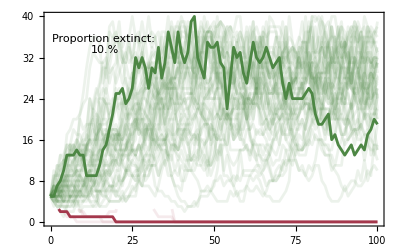

```mathematica
Show[ListLinePlot[extinct3,PlotStyle->Directive[MyCol[[1]],Opacity[0.1]]],
ListLinePlot[extant3,PlotStyle->Directive[MyCol[[4]],Opacity[0.1]]],ListLinePlot[extinct3[[1]],PlotStyle->MyCol[[1]]],
ListLinePlot[extant3[[1]],PlotStyle->MyCol[[4]]],PlotRange->All,Epilog->Inset["Proportion extinct: \n"<>ToString[Length[extinct3]/50*100.0]<>"%",Scaled[{0.18,0.85}]]]
```